# Gráficas del modelo

## Comunicación con NetLogo

```mathematica
<<NetLogo`
If[$OperatingSystem =="Windows",
$NLHome = "C:\\Program Files\\NetLogo 6.1.0\\";
,
$NLHome = "/opt/netlogo";
];
NLStart[$NLHome]
```

### Ejemplo:

```mathematica
NLLoadModel[FileNameJoin[{NotebookDirectory[],"CorredorMariposas.nlogo"}]]
```

```mathematica
NLCommand["setup"];
```

```mathematica
NLCommand["set q",0.1];
```

```mathematica
NLDoCommand["go",1001]
```

```mathematica
NLReport["final-corridor-width"]
```

48.2418

## Cálculo de anchura de corredor

```mathematica
CalculateCorridorWidth[q_]:=Block[{},
If[!ValueQ[$LoadedModel],
$LoadedModel = FileNameJoin[{NotebookDirectory[],"CorredorMariposas.nlogo"}];
NLLoadModel[$LoadedModel]
];
NLCommand["setup"];
NLCommand["set q",q];
NLDoCommand["go",1001];

NLReport["final-corridor-width"]
];
CalculateAverageCorridorWidth[q_,n_]:=Mean[Table[CalculateCorridorWidth[q],n]];
```

```mathematica
corridorWidthVsQ = Table[{q,CalculateAverageCorridorWidth[q,5]},{q,0,1,0.005}];
```

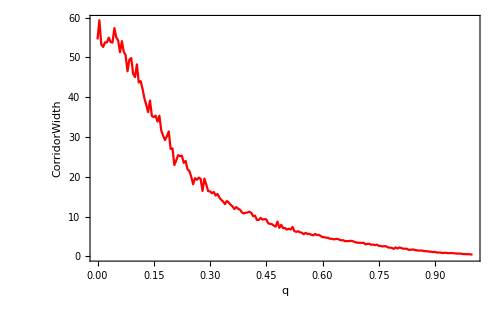

```mathematica
(* Opciones de estilo *)
smallFontSize = 13;
bigFontSize = 15;
plotSize = 500;

ListLinePlot[
corridorWidthVsQ,
PlotTheme->"Monochrome",
FrameLabel->{Style["q",bigFontSize], Style["CorridorWidth",bigFontSize]}, 
ImageSize->plotSize,
BaseStyle->FontSize->smallFontSize,
PlotMarkers->None,
PlotStyle->Red,
Frame->True
]
```